```mathematica
(* First time MaTeX config *)
Needs["PacletManager`"]
ResourceFunction["MaTeXInstall"][](* Tex instalation and Ghostscript required*)
ConfigureMaTeX["pdfLaTeX" -> "C:\\Users\\Sergio\\AppData\\Local\\Programs\\MiKTeX\\miktex\\bin\\x64\\pdflatex.exe", "Ghostscript"->"C:\\Program Files\\gs\\gs10.04.0\\bin\\gswin64c.exe"]
```

PacletObject[…]

{CacheSize→100,WorkingDirectory→Automatic,pdfLaTeX→C:\Users\Sergio\AppData\Local\Programs\MiKTeX\miktex\bin\x64\pdflatex.exe,Ghostscript→C:\Program Files\gs\gs10.04.0\bin\gswin64c.exe}

```mathematica
Needs["MaTeX`"] (* everytime load MaTeX for TeX and test it*)
<<MaTeX`
MaTeX["x^2 + \\sin(x)"]
```

-Graphics-

```mathematica
(* values provided for the model *)
constPSI = -1.43 
b=5.39
psillist ={0.0,0.1,0.2, 0.3, 0.4, 0.5, 0.6, 0.7} 
k1 = 0.005 (* units doesnt matter *)
k2 = 0.0016 (* units doesnt matter *)
Topt = 298 (* units doesnt matter *)
psil0 = -4.5 (* units doesnt matter *)
psil1 = -0.05 (* units doesnt matter *)
Dx = 0.0077 (* g /kg -->kg/kg *)
RH=0.4  (* percentage as a number from 0 to 1 *)
p0=0.1013 (*units MPa*)
gamma = 9.81 (* kg /m^3 *)
```

-1.43

5.39

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7}

0.005

0.0016

298

-4.5

-0.05

0.0077

0.4

0.1013

9.81

```mathematica
Evap[gsrp_, psis_,psil_]= gsrp * (psis-psil)
```

gsrp (-psil+psis)

```mathematica
gsrp[gsr_, gp_]= (gsr*gp)/(gsr+gp)
```

```mathematica
(gp gsr)/(gp+gsr)
```

```mathematica
gsr[K_] = K/(gammaw*lsr)
```

K/(gammaw lsr)

```mathematica
lsr[]
```

```mathematica
gsa[gs_,ga_]=(gs*ga)/(gs+ga)
```

(ga gs)/(ga+gs)

```mathematica
gs[gsmax_,fPAR_ ,fTa_, fpsil_,fD_]= gsmax*fPAR*fTa*fpsil*fD
```

fD fPAR fpsil fTa gsmax

```mathematica
psis[s_]= constPSI*s^(-b)
```

-1.43/s^5.39

```mathematica
fphi[phi_]= 1-Exp[-k1*phi]
```

1-ⅇ^(-0.005 phi)

```mathematica
1-ⅇ^(-k1 phi)
```

1-ⅇ^(-0.005 phi)

```mathematica
fTa[Ta_]=1-k2*(Ta-Topt)^2
```

1-0.0016 (-298+Ta)^2

```mathematica
fpsil[psil_]=(psil-psil0)/(psil1-psil0)
```

0.224719 (4.5+psil)

```mathematica
fD[D_]= 1 / (1 + (D/Dx))
```

1/(1+129.87 D)

```mathematica
Deficit[VPD_]=(0.622/p0)*VPD
```

(0.622 VPD)/p0

```mathematica
VPD[esa_]= esa-e
```

esa-0.4 esaT

```mathematica
e =RH*esa
```

0.4 esa

```mathematica
esa[T_]=6.1094*Exp[17.625*(T-243.04)/T]
```

6.1094 ⅇ^((17.625 (-243.04+T))/T)

```mathematica
Efinal[psil_, s_] = Evap[gsrp[gsr, gp],psis[],psil]
```

Evap[gsrp[gsr,gp],psis[],psil]

```mathematica
fphiplot=Plot[
fphi[phi],{phi,0,800},
PlotLabel->MaTeX["f_\\phi(\\phi)"],
AxesLabel->{MaTeX["\\phi"],MaTeX["f_\\phi"]} ];
```

```mathematica
fTaplot=Plot[
fTa[Ta], {Ta,273.15,313.15},
PlotLabel->MaTeX["f_{T_a}(T_a)"],
AxesLabel->{MaTeX["T_a"],MaTeX["f_{T_a}"]} ];
```

```mathematica
fDplot=Plot[
fD[D],{D,0,0.05},
PlotLabel->MaTeX["f_{D}(D)"],
AxesLabel->{MaTeX["D"],MaTeX["f_{D}"]} ];
```

```mathematica
fpsilplot=Plot[
fpsil[psil],{psil, psil0,psil1},
PlotLabel->MaTeX["f_{\\psi_l}(\\psi_l)"],
AxesLabel->{MaTeX["\\psi_l"],MaTeX["f_{\\psi_l}"]} ];
```

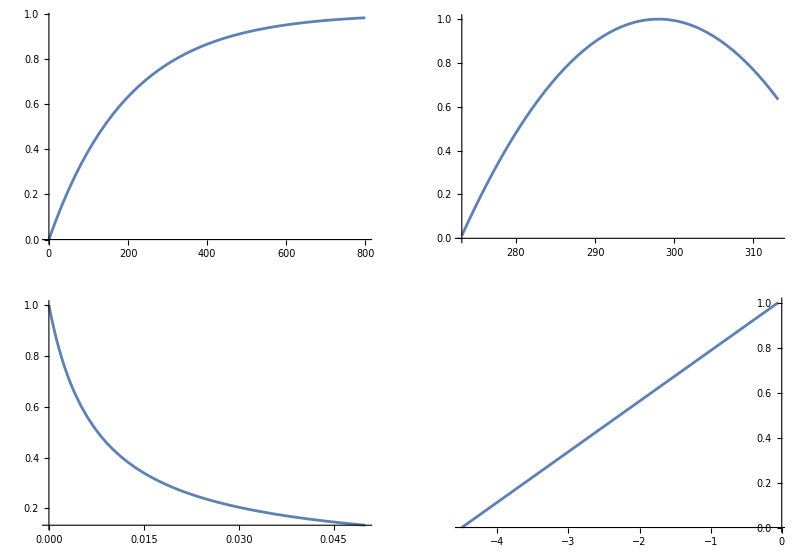

```mathematica
GraphicsGrid[{{fphiplot,fTaplot},{fDplot,fpsilplot}}]
```

```mathematica
Export["C:\\Users\\Sergio\\Documents\\GitHub\\ecohydrology\\Assignments\\Ass4\\.png",%52,"PNG"]
```

C:\Users\Sergio\Documents\GitHub\ecohydrology\Assignments\Ass4\.png